# Leads connected to 1 - 10 and 41 to 50

# a1 and a3

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
leads[10]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+301]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,37,1,37],s[38,50,38,50]],concentration],RandomSample[Join[s[1,37,38,50],s[38,50,1,37]],total-concentration]],First],1000]
```

```mathematica
ll[x_]:=ListLinePlot[Table[{x,y},{y,0,50}],PlotStyle->Red]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,41,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[41;;50,41;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

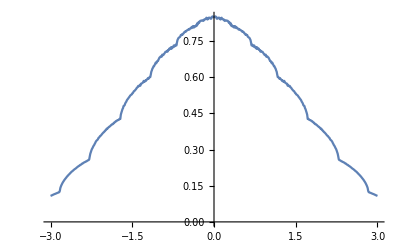

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,10][[10,10]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=10,abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
Table[Mean[ParallelTable[CA[1.2,0.0001,1,0,1,50,conc,n],{n,500}]],{conc,5,45,5}]
```

{2.19257,2.1139,1.90187,1.78898,1.76768,1.74587,1.72798,1.62465,1.57716}

```mathematica
Table[Export["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,50,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,5,45,5}]
```

5

10

15

20

25

30

35

40

45

{/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_5_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_10_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_15_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_20_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_25_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_30_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_35_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_40_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_45_.dat}

```mathematica
transmission=Table[{x,Import["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/3*3/leads_1_10_and_41_50/50_ϵ1_conc_diag_"<>ToString[x]<>"_.dat"]},{x,Range[5,45,5]}]
```

{{5,{{0.,6.59324},{0.01,5.75406},{0.02,5.37201},{0.03,4.94918},{0.04,4.46988},{0.05,4.13502},{0.06,3.57214},{0.07,3.08498},{0.08,4.38492},{0.09,3.41933},{0.1,3.45965},{0.11,3.89347},{0.12,4.27061},{0.13,4.51442},{0.14,4.59727},272,{2.87,1.1699},{2.88,1.06288},{2.89,0.959552},{2.9,1.01327},{2.91,1.06217},{2.92,1.13249},{2.93,1.15169},{2.94,1.07366},{2.95,1.05595},{2.96,1.12949},{2.97,1.2266},{2.98,1.32604},{2.99,1.26676},{3.,1.28379}}},7,{45,{1}}}
 |  |  |  |

```mathematica
input[conc_]:=input[conc]= Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,50,conc,n]},{ω,Range[0,3,0.01]}],{n,100}]
```

```mathematica
misfit[x_,y_,n_,conc_]:=Module[{m5=input[conc][[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,9}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Abs[Table[misfit[3,0.1,n,40][[2]][[1]]-40,{n,100}]]/40//Mean
```

97/800

```mathematica
N[97/800]
```

0.12125

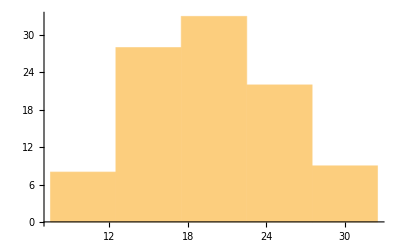

```mathematica
Histogram[%23]
```

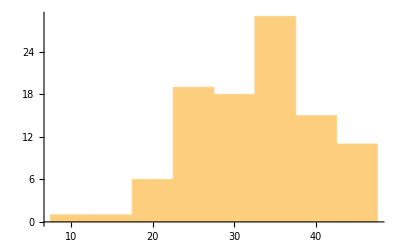

```mathematica
Histogram[%38]
```

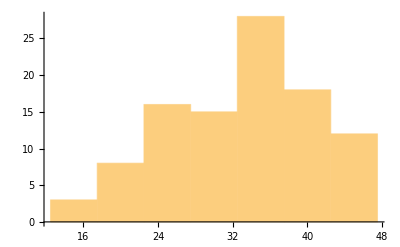

```mathematica
Histogram[%36]
```